```mathematica
NS["fmri_alzheimer"]
```

```mathematica
(* Load data given by Claudia *)
relevant=Range[28];
datah=Import["claudia_RGS_graphprop22_Con.txt","CSV"];
datah=datah[[relevant,2;;]];

smean=Mean[T@datah];snorm=1/Std[T@datah];
datah=N[snorm*(datah-smean)];

dataa=Import["claudia_RGS_graphprop22_AD.txt","CSV"];
quantities=T[dataa][[1]][[relevant]];
dataa=dataa[[relevant,2;;]];
dataa=N[snorm*(dataa-smean)];

datam=Import["claudia_RGS_graphprop22_MCI.txt","CSV"];
datam=datam[[relevant,2;;]];
datam=N[snorm*(datam-smean)];

nq=Length[quantities];
health={1,2,3};
data[1]=datah;data[2]=dataa;data[3]=datam;
```

```mathematica
{Range[28],quantities}//T//MF
```

(1 | graphweights1
2 | shortest path1
3 | cluster coeff1.
4 | weighted degree1
5 | normalized weighted degree1
6 | node size
7 | closeness centrality1
8 | modularity
9 | graphweights2
10 | shortest path2
11 | cluster coeff.2
12 | weighted degree2
13 | normalized weighted degree2
14 | closeness centrality2
15 | graphweights3
16 | shortest path3
17 | cluster coeff.3
18 | weighted degree3
19 | normalized weighted degree3
20 | closeness centrality3
21 | graphweights4
22 | shortest path4
23 | cluster coeff.4
24 | weighted degree4
25 | normalized weighted degree4
26 | closeness centrality4
27 | mean across time
28 | std across time)

```mathematica
quant=quantities;
delr={0,0,0};
Do[datatest=data[ii][[;;,;;]];nit=Length[T[datatest]];
meanst=Mean@T@datatest;
dscattert=(nit+1)/nit*(datatest-meanst).T[datatest-meanst]; 
delr[[ii]]=Ordering[Abs@Diagonal[Minors[dscattert]],-9],{ii,3}];
delr=Sort[Union@Flatten@delr,Greater];

Do[data[ii]=Drop[data[ii],{delr[[jjj]]}],
{jjj,Length@delr},{ii,3}];
Do[quant=Drop[quant,{delr[[jjj]]}];,{jjj,Length@delr}];
```

```mathematica
delr
```

{28,27,26,25,22,19,18,17,14,13,11,10,7,6,5,4}

```mathematica
quant
```

{graphweights1,shortest path1,cluster coeff1.,modularity,graphweights2,weighted degree2,graphweights3,shortest path3,closeness centrality3,graphweights4,cluster coeff.4,weighted degree4}

```mathematica
relevant=Complement[Range[28],delr]
```

{1,2,3,8,9,12,15,16,20,21,23,24}

```mathematica
quantities[[relevant]]
```

{graphweights1,shortest path1,cluster coeff1.,modularity,graphweights2,weighted degree2,graphweights3,shortest path3,closeness centrality3,graphweights4,cluster coeff.4,weighted degree4}

```mathematica
relevant=Sort@{1,9,15,21,2,10,16,3,11,17,23,4,12,18,24,7,14,20,26,8}
```

{1,2,3,4,7,8,9,10,11,12,14,15,16,17,18,20,21,23,24,26}

```mathematica
{Range[28],quantities}//T//MF
```

(1 | graphweights1
2 | shortest path1
3 | cluster coeff1.
4 | weighted degree1
5 | normalized weighted degree1
6 | node size
7 | closeness centrality1
8 | modularity
9 | graphweights2
10 | shortest path2
11 | cluster coeff.2
12 | weighted degree2
13 | normalized weighted degree2
14 | closeness centrality2
15 | graphweights3
16 | shortest path3
17 | cluster coeff.3
18 | weighted degree3
19 | normalized weighted degree3
20 | closeness centrality3
21 | graphweights4
22 | shortest path4
23 | cluster coeff.4
24 | weighted degree4
25 | normalized weighted degree4
26 | closeness centrality4
27 | mean across time
28 | std across time)

```mathematica
{
```

```mathematica
quant=quantities;
Do[delr={0,0,0};
Do[datatest=data[ii][[;;,;;]];nit=Length[T[datatest]];
meanst=Mean@T@datatest;
dscattert=(nit+1)/nit*(datatest-meanst).T[datatest-meanst]; 
delr[[ii]]=Ordering[Abs@Diagonal[Minors[dscattert]],-1],{ii,3}];
delr=Sort[Union@Flatten@delr,Greater];
Print[delr];

Print[Dimensions[data[1]]];
Do[data[ii]=Drop[data[ii],{delr[[jjj]]}],
{jjj,Length@delr},{ii,3}];
Print[Dimensions[data[1]]];
Do[quant=Drop[quant,{delr[[jjj]]}];,{jjj,Length@delr}];
,{jj,5}]
```

```mathematica
quant
```

{graphweights1,shortest path1,cluster coeff1.,closeness centrality1,modularity,graphweights2,shortest path2,graphweights3,shortest path3,cluster coeff.3,weighted degree3,normalized weighted degree3,closeness centrality3,graphweights4,shortest path4,normalized weighted degree4,closeness centrality4}

```mathematica
ClearAll[tabeg,tabinc];
Do[datatest=data[ii][[;;,;;]];nit=Length[T[datatest]];
meanst=Mean@T@datatest;
dscattert=(nit+1)/nit*(datatest-meanst).T[datatest-meanst]; 
eg=Eigensystem[dscattert];
tabeg[ii]=Table[orde=Ordering[Abs[eg[[2]][[i]]],-2];Flatten@{i,Log[10,Abs[eg[[1,i]]]],Abs[eg[[2]][[i,orde]]],quantities[[orde]]},{i,nq}]//MF;
tabinc[ii]=Table[Union@Flatten@Table[orde=Ordering[Abs[eg[[2]][[i]]],-2];Flatten@{j,quantities[[orde]]},{i,j}],{j,28}]
,{ii,3}]
```

```mathematica
Abs@Diagonal[Minors[dscattert]]
```

{4.11812×10^-170,3.36743×10^-170,2.13933×10^-169,7.03317×10^-168,3.69826×10^-168,3.39077×10^-168,6.1172×10^-169,2.41988×10^-169,1.82225×10^-169,4.71475×10^-168,4.91532×10^-166,2.16147×10^-169,2.71721×10^-169,9.64367×10^-170,1.18364×10^-170,4.67805×10^-169,1.37556×10^-169,9.40355×10^-169,5.23481×10^-169,1.23832×10^-169,3.20595×10^-170,9.0204×10^-169,8.30998×10^-170,7.7156×10^-170,2.34012×10^-172,1.87509×10^-168,2.83013×10^-169,5.21333×10^-169}

```mathematica
Ordering[Abs@Diagonal[Minors[dscattert]],-1]
```

{11}

```mathematica
tabeg[1]
```

(1 | 2.50843 | 0.256618 | 0.264678 | graphweights4 | closeness centrality2
2 | 2.16854 | 0.266961 | 0.277464 | weighted degree1 | normalized weighted degree1
3 | 1.91743 | 0.418412 | 0.419484 | normalized weighted degree2 | normalized weighted degree4
4 | 1.8921 | 0.429665 | 0.441548 | shortest path3 | shortest path4
5 | 1.52298 | 0.52667 | 0.680695 | mean across time | std across time
6 | 1.4394 | 0.353789 | 0.594185 | modularity | mean across time
7 | 1.20005 | 0.430081 | 0.639788 | modularity | node size
8 | 1.15274 | 0.305472 | 0.320473 | graphweights3 | closeness centrality3
9 | 1.04862 | 0.41638 | 0.503117 | modularity | std across time
10 | 0.985974 | 0.328467 | 0.386305 | weighted degree4 | std across time
11 | 0.709534 | 0.345502 | 0.412001 | normalized weighted degree2 | shortest path1
12 | 0.514212 | 0.366455 | 0.406098 | closeness centrality3 | node size
13 | 0.326349 | 0.381894 | 0.40861 | graphweights2 | normalized weighted degree2
14 | 0.267216 | 0.353936 | 0.473521 | modularity | normalized weighted degree2
15 | -0.336371 | 0.3431 | 0.360255 | shortest path1 | closeness centrality4
16 | -0.372703 | 0.406674 | 0.4179 | shortest path3 | normalized weighted degree4
17 | -0.668095 | 0.420631 | 0.481776 | closeness centrality3 | closeness centrality2
18 | -0.910305 | 0.410398 | 0.461593 | cluster coeff.2 | closeness centrality4
19 | -1.2449 | 0.383888 | 0.50214 | cluster coeff.3 | weighted degree2
20 | -1.4818 | 0.410258 | 0.571699 | graphweights4 | graphweights3
21 | -1.92354 | 0.315095 | 0.335046 | weighted degree3 | shortest path4
22 | -2.34836 | 0.461752 | 0.568338 | cluster coeff1. | closeness centrality1
23 | -2.55119 | 0.40964 | 0.438869 | normalized weighted degree3 | cluster coeff.4
24 | -2.72505 | 0.362976 | 0.438313 | normalized weighted degree4 | closeness centrality1
25 | -3.33 | 0.377473 | 0.43106 | weighted degree1 | shortest path2
26 | -14.2809 | 0.626351 | 0.772672 | weighted degree1 | graphweights1
27 | -14.6179 | 0.528961 | 0.722431 | weighted degree4 | weighted degree3
28 | -15.387 | 0.433358 | 0.484277 | closeness centrality1 | weighted degree1)

```mathematica
tabeg[2]
```

(1 | 4.71659 | 0.0910702 | 0.988603 | cluster coeff.4 | weighted degree1
2 | 3.68185 | 0.456823 | 0.66803 | closeness centrality3 | cluster coeff.4
3 | 1.87744 | 0.438296 | 0.539422 | modularity | shortest path4
4 | 1.42057 | 0.499236 | 0.69963 | shortest path4 | std across time
5 | 1.21418 | 0.490399 | 0.53307 | modularity | std across time
6 | 0.900382 | 0.498102 | 0.537367 | normalized weighted degree2 | mean across time
7 | 0.728903 | 0.356072 | 0.383239 | graphweights3 | normalized weighted degree2
8 | 0.469488 | 0.38461 | 0.546149 | shortest path1 | mean across time
9 | 0.120578 | 0.514493 | 0.631985 | modularity | normalized weighted degree1
10 | -0.149615 | 0.434454 | 0.673604 | mean across time | shortest path3
11 | -0.57186 | 0.424408 | 0.455762 | cluster coeff.2 | shortest path2
12 | -1.14706 | 0.431724 | 0.500453 | normalized weighted degree3 | graphweights3
13 | -1.89654 | 0.425644 | 0.507948 | normalized weighted degree4 | cluster coeff.2
14 | -11.8094 | 0.336199 | 0.820887 | closeness centrality3 | closeness centrality4
15 | -12.3683 | 0.383485 | 0.49449 | shortest path2 | shortest path3
16 | -12.8093 | 0.484238 | 0.50755 | closeness centrality3 | cluster coeff.4
17 | -12.9716 | 0.38147 | 0.395165 | closeness centrality2 | closeness centrality3
18 | -13.3009 | 0.436061 | 0.549359 | normalized weighted degree4 | cluster coeff.3
19 | -13.5655 | 0.431444 | 0.488428 | closeness centrality1 | weighted degree2
20 | -13.5843 | 0.449603 | 0.45284 | cluster coeff.2 | normalized weighted degree4
21 | -13.9452 | 0.387373 | 0.575482 | shortest path1 | graphweights4
22 | -14.0554 | 0.423807 | 0.525263 | graphweights2 | graphweights4
23 | -14.3864 | 0.566459 | 0.789444 | weighted degree3 | weighted degree4
24 | -14.6858 | 0.506315 | 0.655366 | weighted degree4 | weighted degree3
25 | -14.7487 | 0.491787 | 0.648654 | closeness centrality1 | graphweights2
26 | -14.7675 | 0.448701 | 0.500545 | weighted degree2 | cluster coeff1.
27 | -15.0238 | 0.50267 | 0.683459 | weighted degree2 | cluster coeff1.
28 | -15.7364 | 0.374651 | 0.701327 | graphweights2 | graphweights1)

```mathematica
tabeg[3]
```

(1 | 5.39851 | 0.0104412 | 0.999658 | graphweights4 | weighted degree1
2 | 2.07601 | 0.348105 | 0.520963 | closeness centrality2 | graphweights4
3 | 1.72417 | 0.462373 | 0.684382 | std across time | modularity
4 | 1.57868 | 0.341252 | 0.816609 | modularity | std across time
5 | 1.26632 | 0.473576 | 0.474635 | shortest path2 | shortest path1
6 | 0.995718 | 0.404322 | 0.725484 | normalized weighted degree2 | mean across time
7 | 0.73971 | 0.375337 | 0.544665 | normalized weighted degree3 | normalized weighted degree2
8 | 0.555389 | 0.415499 | 0.561573 | mean across time | normalized weighted degree1
9 | 0.182865 | 0.356235 | 0.386577 | shortest path4 | node size
10 | 0.0882216 | 0.404317 | 0.577216 | closeness centrality2 | shortest path3
11 | -0.537166 | 0.325342 | 0.42721 | normalized weighted degree1 | cluster coeff1.
12 | -0.868775 | 0.362294 | 0.486346 | closeness centrality2 | graphweights2
13 | -0.962405 | 0.331379 | 0.495065 | weighted degree2 | cluster coeff.2
14 | -1.29576 | 0.393933 | 0.418678 | cluster coeff1. | normalized weighted degree3
15 | -1.61299 | 0.444375 | 0.573562 | normalized weighted degree3 | weighted degree2
16 | -12.0376 | 0.447848 | 0.624501 | graphweights4 | closeness centrality4
17 | -13.1377 | 0.360019 | 0.420685 | cluster coeff.2 | cluster coeff.3
18 | -13.2895 | 0.457304 | 0.48527 | closeness centrality4 | graphweights3
19 | -13.4624 | 0.450458 | 0.467937 | node size | weighted degree2
20 | -13.7071 | 0.440868 | 0.442494 | normalized weighted degree4 | closeness centrality1
21 | -13.7713 | 0.3285 | 0.652788 | shortest path4 | cluster coeff.4
22 | -13.8621 | 0.390793 | 0.417013 | shortest path1 | cluster coeff.3
23 | -14.0313 | 0.467744 | 0.515986 | closeness centrality1 | weighted degree4
24 | -14.2084 | 0.322887 | 0.582835 | normalized weighted degree3 | closeness centrality3
25 | -14.2623 | 0.430693 | 0.679447 | graphweights1 | weighted degree4
26 | -14.2709 | 0.33928 | 0.437811 | cluster coeff.3 | shortest path2
27 | -15.0471 | 0.468944 | 0.610743 | cluster coeff1. | graphweights1
28 | -15.863 | 0.207766 | 0.932751 | graphweights1 | weighted degree3)

```mathematica
Union@Flatten@Table[tabinc[ii][[12]],{ii,3}]
```

{12,closeness centrality2,closeness centrality3,cluster coeff.2,cluster coeff.4,graphweights2,graphweights3,graphweights4,mean across time,modularity,node size,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1}

```mathematica
Union@Flatten@Table[tabinc[ii][[13]],{ii,3}]
```

{13,closeness centrality2,closeness centrality3,cluster coeff.2,cluster coeff.4,graphweights2,graphweights3,graphweights4,mean across time,modularity,node size,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2}

```mathematica
tabinc[1][[14]]
```

{14,closeness centrality2,closeness centrality3,cluster coeff.2,graphweights2,graphweights3,graphweights4,mean across time,modularity,node size,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path3,std across time,weighted degree1}

```mathematica
tabinc[3][[14]]
```

{14,closeness centrality2,closeness centrality4,cluster coeff1.,graphweights2,graphweights3,graphweights4,mean across time,modularity,node size,normalized weighted degree1,shortest path1,shortest path2,shortest path3,std across time,weighted degree2}

```mathematica
Table[Union@Flatten@Table[orde=Ordering[eg[[2]][[i]],-2];Flatten@{j,quantities[[orde]]},{i,j}],{j,28}]
```

```mathematica
eg=Eigensystem[dscattert];
```

```mathematica
Table[{i,eg[[1,i]]},{i,28}]
```

{{1,9.07271×10^13},{2,3.88881×10^6},{3,2.06381×10^6},{4,830673.},{5,4684.14},{6,654.156},{7,146.53},{8,17.4991},{9,1.82558},{10,1.66836},{11,0.139599},{12,0.00125168},{13,0.000141408},{14,6.48502×10^-6},{15,-2.23442×10^-10},{16,-2.34781×10^-11},{17,-1.00963×10^-12},{18,-1.58636×10^-13},{19,2.63366×10^-14},{20,2.04065×10^-15},{21,1.73788×10^-15},{22,3.69811×10^-16},{23,-3.41393×10^-17},{24,-2.47274×10^-17},{25,-2.17904×10^-17},{26,1.06318×10^-18},{27,4.12929×10^-19},{28,3.62865×10^-21}}

```mathematica
eg[[1]]
```

{9.07271×10^13,3.88881×10^6,2.06381×10^6,830673.,4684.14,654.156,146.53,17.4991,1.82558,1.66836,0.139599,0.00125168,0.000141408,6.48502×10^-6,-2.23442×10^-10,-2.34781×10^-11,-1.00963×10^-12,-1.58636×10^-13,2.63366×10^-14,2.04065×10^-15,1.73788×10^-15,3.69811×10^-16,-3.41393×10^-17,-2.47274×10^-17,-2.17904×10^-17,1.06318×10^-18,4.12929×10^-19,3.62865×10^-21}

```mathematica
Table[orde=Ordering[eg[[2]][[i]],-2];Flatten@{i,Log[10,Abs[eg[[1,i]]]],eg[[2]][[i,orde]],quantities[[orde]]},{i,nq}]//MF
```

(1 | 13.9577 | 0.000011077 | 1. | weighted degree4 | std across time
2 | 6.58982 | 0.0454128 | 0.797081 | weighted degree3 | weighted degree4
3 | 6.31467 | 0.512581 | 0.843224 | weighted degree4 | shortest path4
4 | 5.91943 | 0.00499341 | 0.0134767 | node size | shortest path4
5 | 3.67063 | 0.106179 | 0.900116 | weighted degree1 | node size
6 | 2.81568 | 0.0604738 | 0.116127 | weighted degree4 | shortest path3
7 | 2.16593 | 0.184287 | 0.947773 | shortest path1 | shortest path3
8 | 1.24302 | 0.37944 | 0.677302 | weighted degree2 | shortest path2
9 | 0.2614 | 0.0592834 | 0.420926 | node size | shortest path1
10 | 0.22229 | 0.131012 | 0.369987 | shortest path1 | shortest path2
11 | -0.855119 | 0.537405 | 0.809537 | weighted degree1 | shortest path1
12 | -2.90251 | 0.16402 | 0.342862 | shortest path1 | modularity
13 | -3.84953 | 0.00525692 | 0.00738562 | normalized weighted degree3 | weighted degree2
14 | -5.18809 | 0.17082 | 0.270295 | normalized weighted degree1 | cluster coeff1.
15 | -9.65084 | 0.00317257 | 0.922737 | cluster coeff1. | closeness centrality4
16 | -10.6293 | 0.385153 | 0.921373 | closeness centrality4 | normalized weighted degree4
17 | -11.9958 | 0.187864 | 0.24516 | graphweights4 | graphweights1
18 | -12.7996 | 0.205102 | 0.266305 | modularity | closeness centrality1
19 | -13.5794 | 0.192993 | 0.3875 | cluster coeff1. | graphweights1
20 | -14.6902 | 0.0906777 | 0.118749 | cluster coeff1. | graphweights1
21 | -14.76 | 0.129814 | 0.680583 | graphweights1 | closeness centrality3
22 | -15.432 | 0.213998 | 0.310577 | modularity | graphweights1
23 | -16.4667 | 0.0102283 | 0.208838 | closeness centrality1 | graphweights2
24 | -16.6068 | 0.135514 | 0.708726 | normalized weighted degree2 | cluster coeff.3
25 | -16.6617 | 0.42476 | 0.502009 | cluster coeff.2 | graphweights3
26 | -17.9734 | 0.0428127 | 0.0961897 | normalized weighted degree2 | closeness centrality1
27 | -18.3841 | 0.131235 | 0.555164 | cluster coeff.2 | graphweights3
28 | -20.4403 | 0.209282 | 0.514231 | closeness centrality2 | graphweights3)

```mathematica
Ordering[eg[[2]][[1]],2]
```

{24,18}

```mathematica
eg[[2]][[1]]
```

{-3.67953×10^-9,7.02347×10^-8,-4.37873×10^-9,-3.70101×10^-9,1.66463×10^-9,-1.85604×10^-6,-3.47811×10^-9,-1.90031×10^-9,-4.03113×10^-10,4.99393×10^-8,-7.89499×10^-12,-1.75203×10^-6,4.93967×10^-10,-6.87183×10^-11,-1.70028×10^-10,1.15275×10^-7,-9.11097×10^-13,-0.0000252301,1.00962×10^-10,-1.55976×10^-12,-8.35649×10^-11,1.30433×10^-6,-1.13086×10^-13,-0.000601312,3.3736×10^-11,-6.7896×10^-13,0.0000633797,1.}

```mathematica
eg[[2]][[1,{24,18}]]
```

{-0.000601312,-0.0000252301}

```mathematica
quantities
```

{graphweights1,shortest path1,cluster coeff1.,weighted degree1,normalized weighted degree1,node size,closeness centrality1,modularity,graphweights2,shortest path2,cluster coeff.2,weighted degree2,normalized weighted degree2,closeness centrality2,graphweights3,shortest path3,cluster coeff.3,weighted degree3,normalized weighted degree3,closeness centrality3,graphweights4,shortest path4,cluster coeff.4,weighted degree4,normalized weighted degree4,closeness centrality4,mean across time,std across time}

```mathematica
Table[Union@Flatten@Table[orde=Ordering[eg[[2]][[i]],-2];Flatten@{j,quantities[[orde]]},{i,j}],{j,28}]
```

{{1,mean across time,std across time},{2,mean across time,std across time,weighted degree3,weighted degree4},{3,mean across time,shortest path4,std across time,weighted degree3,weighted degree4},{4,mean across time,shortest path3,shortest path4,std across time,weighted degree3,weighted degree4},{5,mean across time,shortest path2,shortest path3,shortest path4,std across time,weighted degree3,weighted degree4},{6,mean across time,shortest path2,shortest path3,shortest path4,std across time,weighted degree2,weighted degree3,weighted degree4},{7,mean across time,shortest path2,shortest path3,shortest path4,std across time,weighted degree2,weighted degree3,weighted degree4},{8,mean across time,shortest path2,shortest path3,shortest path4,std across time,weighted degree2,weighted degree3,weighted degree4},{9,mean across time,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree2,weighted degree3,weighted degree4},{10,mean across time,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree2,weighted degree3,weighted degree4},{11,closeness centrality1,mean across time,normalized weighted degree1,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree2,weighted degree3,weighted degree4},{12,closeness centrality1,cluster coeff1.,mean across time,normalized weighted degree1,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{13,closeness centrality1,cluster coeff1.,mean across time,normalized weighted degree1,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{14,closeness centrality1,cluster coeff1.,mean across time,normalized weighted degree1,normalized weighted degree2,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{15,closeness centrality1,cluster coeff1.,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{16,closeness centrality1,cluster coeff1.,graphweights1,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{17,closeness centrality1,cluster coeff1.,graphweights1,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{18,closeness centrality1,cluster coeff1.,graphweights1,graphweights3,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{19,closeness centrality1,closeness centrality2,cluster coeff1.,graphweights1,graphweights3,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{20,closeness centrality1,closeness centrality2,cluster coeff1.,graphweights1,graphweights3,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{21,closeness centrality1,closeness centrality2,cluster coeff1.,graphweights1,graphweights3,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{22,closeness centrality1,closeness centrality2,cluster coeff1.,graphweights1,graphweights3,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{23,closeness centrality1,closeness centrality2,cluster coeff1.,cluster coeff.2,graphweights1,graphweights3,graphweights4,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{24,closeness centrality1,closeness centrality2,cluster coeff1.,cluster coeff.2,graphweights1,graphweights3,graphweights4,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{25,closeness centrality1,closeness centrality2,closeness centrality3,cluster coeff1.,cluster coeff.2,graphweights1,graphweights3,graphweights4,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{26,closeness centrality1,closeness centrality2,closeness centrality3,closeness centrality4,cluster coeff1.,cluster coeff.2,graphweights1,graphweights3,graphweights4,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{27,closeness centrality1,closeness centrality2,closeness centrality3,closeness centrality4,cluster coeff1.,cluster coeff.2,graphweights1,graphweights3,graphweights4,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4},{28,closeness centrality1,closeness centrality2,closeness centrality3,closeness centrality4,cluster coeff1.,cluster coeff.2,cluster coeff.3,graphweights1,graphweights3,graphweights4,mean across time,modularity,normalized weighted degree1,normalized weighted degree2,normalized weighted degree3,normalized weighted degree4,shortest path1,shortest path2,shortest path3,shortest path4,std across time,weighted degree1,weighted degree2,weighted degree3,weighted degree4}}

```mathematica
(*-----------------------------------------------------------*)
```

```mathematica
(* Load data given by Claudia *)
(*relevant={7,3,27,28,2,10,16,22,4,12,18,24};*)
(*relevant=Range[28];*)

datah=Import["claudia_RGS_graphprop22_Con.txt","CSV"];
datah=datah[[relevant,2;;]];

smean=Mean[T@datah];snorm=1/Std[T@datah];
datah=N[snorm*(datah-smean)];

dataa=Import["claudia_RGS_graphprop22_AD.txt","CSV"];
quantities=T[dataa][[1]][[relevant]];
dataa=dataa[[relevant,2;;]];
dataa=N[snorm*(dataa-smean)];

datam=Import["claudia_RGS_graphprop22_MCI.txt","CSV"];
datam=datam[[relevant,2;;]];
datam=N[snorm*(datam-smean)];

nq=Length[quantities];
health={1,2,3};
data[1]=datah;data[2]=dataa;data[3]=datam;
```

```mathematica
ClearAll[nindiv,means,dscatter,idscatter,istdmatrix];
Do[nindiv[i]=Length[T[data[i]]];
means[i]=Mean@T@data[i];
dscatter[i]=(nindiv[i]+1)/nindiv[i]*(data[i]-means[i]).T[data[i]-means[i]]; 
idscatter[i]=Inverse[dscatter[i]];
istdmatrix[i]=Inverse[dscatter[i]/(nindiv[i]-1-nq)];
,{i,health}];
```

```mathematica
quantities
```

{graphweights1,shortest path1,cluster coeff1.,modularity,graphweights2,weighted degree2,graphweights3,shortest path3,closeness centrality3,graphweights4,cluster coeff.4,weighted degree4}

```mathematica
dscatter[3]//MF
```

(14.9058 | -14.1056 | 13.9516 | -12.2061 | 18.6423 | 6.57259 | 16.577 | -4.53255 | 13.5708 | 26.5331 | 4.14026 | 1.41457
-14.1056 | 17.5462 | -13.3175 | 14.1782 | -15.1386 | -6.06959 | -12.1065 | 6.76324 | -9.26301 | -18.5231 | -2.86108 | -1.33744
13.9516 | -13.3175 | 13.1428 | -11.1521 | 17.2957 | 6.08197 | 15.3735 | -4.17349 | 12.6986 | 24.6201 | 3.82813 | 1.2983
-12.2061 | 14.1782 | -11.1521 | 39.9815 | -10.9005 | -4.87729 | -5.46521 | 8.32588 | -7.4578 | -13.0308 | -1.79667 | -1.13404
18.6423 | -15.1386 | 17.2957 | -10.9005 | 26.1478 | 8.22497 | 24.8204 | -4.19941 | 20.1868 | 39.1761 | 6.30275 | 1.66574
6.57259 | -6.06959 | 6.08197 | -4.87729 | 8.22497 | 5.90598 | 7.43437 | -1.87867 | 6.24903 | 11.6793 | 1.75449 | 1.61616
16.577 | -12.1065 | 15.3735 | -5.46521 | 24.8204 | 7.43437 | 24.8436 | -2.75516 | 19.6961 | 38.4731 | 6.16725 | 1.466
-4.53255 | 6.76324 | -4.17349 | 8.32588 | -4.19941 | -1.87867 | -2.75516 | 3.85432 | -2.04777 | -4.22408 | -0.527635 | -0.422458
13.5708 | -9.26301 | 12.6986 | -7.4578 | 20.1868 | 6.24903 | 19.6961 | -2.04777 | 17.4738 | 32.055 | 5.08889 | 1.22638
26.5331 | -18.5231 | 24.6201 | -13.0308 | 39.1761 | 11.6793 | 38.4731 | -4.22408 | 32.055 | 61.4728 | 9.72325 | 2.30433
4.14026 | -2.86108 | 3.82813 | -1.79667 | 6.30275 | 1.75449 | 6.16725 | -0.527635 | 5.08889 | 9.72325 | 1.69972 | 0.321375
1.41457 | -1.33744 | 1.2983 | -1.13404 | 1.66574 | 1.61616 | 1.466 | -0.422458 | 1.22638 | 2.30433 | 0.321375 | 0.469385)

```mathematica
Dimensions/@{datah,dataa,datam}
```

{{12,26},{12,14},{12,16}}

```mathematica
Table[{i,quantities[[i]]},{i,nq}]//MF
```

(1 | graphweights1
2 | shortest path1
3 | cluster coeff1.
4 | modularity
5 | graphweights2
6 | weighted degree2
7 | graphweights3
8 | shortest path3
9 | closeness centrality3
10 | graphweights4
11 | cluster coeff.4
12 | weighted degree4)

```mathematica
Sort@quantities
```

{closeness centrality3,cluster coeff1.,cluster coeff.4,graphweights1,graphweights2,graphweights3,graphweights4,modularity,shortest path1,shortest path3,weighted degree2,weighted degree4}

```mathematica
quantities[[{7,3,27,28,2,10,16,22,4,12,18,24}]]
```

{closeness centrality1,cluster coeff1.,mean across time,std across time,shortest path1,shortest path2,shortest path3,shortest path4,weighted degree1,weighted degree2,weighted degree3,weighted degree4}

```mathematica
lnpdf[i_,x_]:=Log[Gamma[(nindiv[i]+1)/2]]-Log[Gamma[(nindiv[i]+1-nq)/2]]-Log[Det[dscatter[i]*Pi]]/2-(nindiv[i]+1)*Log[1+(x-means[i]).idscatter[i].(x-means[i])]/2;
```

```mathematica
lnpdf[2,Range[nq]*0]
```

-47.5456

```mathematica
Do[r95[i]=N@InverseCDF[FRatioDistribution[nq,nindiv[i]+1-nq],95/100],{i,3}]
```

```mathematica
r95[2]
```

8.74464

```mathematica
(* Order of health groups and parameters of the data *)
{health,parnames}=(<<"claudia_test5_mean_names.txt")
```

{{H,C,A},{graph weights,shortest path,cluster coefficient,degree,modularity,number of nodes}}

```mathematica
(* Empirical means and standard deviations *)
meansall=Table[Mean@T@datafull[[i]],{i,3}]//N
```

{{0.627358,1.68921,0.64025,156.341,0.056081,249.615},{0.653689,1.60256,0.663035,147.878,0.0461562,229.667},{0.657526,1.607,0.667931,146.964,0.0409293,224.923}}

```mathematica
stdall=Table[Std@T@datafull[[i]],{i,3}]//N
```

{{0.0923868,0.286423,0.0820397,27.9338,0.0345552,19.2215},{0.085302,0.268161,0.075857,14.9414,0.0303107,26.1831},{0.0809806,0.218788,0.0792804,24.7297,0.01745,30.8482}}

```mathematica
lntstudent[x_,data_]:=Module[{d=Length[T@data],n,dscatter,idscatter},Table[
means[i]=Mean@T@data[i];
(* scatter matrix with numerical factor *)dscatter[i]=(nindiv[i]+1)/nindiv[i]*(data[i]-means[i]).T[data[i]-means[i]]; 
idscatter[i]=Inverse[dscatter[i]];
istdmatrix[i]=Inverse[dscatter[i]/(nindiv[i]-1-nq)];

(* logarithm of t-distribution *)
Log[Gamma[(nindiv[i]+1)/2]]-Log[Gamma[(nindiv[i]+1-nq)/2]]-Log[Det[dscatter[i]*Pi]]/2-(nindiv[i]+1)*Log[1+(x-means[i]).idscatter[i].(x-means[i])]/2,

{i,health}]]
```

```mathematica
lnpdf[2,Range[nq]*0]
```

-1/2 Log[Det[π dscatter[2]]]-Log[Gamma[1/2 (-11+nindiv[2])]]+Log[Gamma[1/2 (1+nindiv[2])]]-1/2 Log[1+{-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2]}.idscatter[2].{-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2],-means[2]}] (1+nindiv[2])

```mathematica
(* Logarithm of predictive distribution {P(x|H,data), P(x|C,data), P(x|A,data)} 
it also calculates and stores expectations and covariances *)
ClearAll[means,istdmatrix,num];lntstudent[x_,data_]:=Module[{health=Length@data,d=Length[T@data],n,dscatter,idscatter},Table[(* number individuals *) n[i]=Length[T[data[[i]]]];num[i]=n[i];
means[i]=Mean@T@data[[i]];
(* scatter matrix with numerical factor *)dscatter[i]=(n[i]+1)/n[i]*(data[[i]]-means[i]).T[data[[i]]-means[i]]; 
idscatter[i]=Inverse[dscatter[i]];
istdmatrix[i]=Inverse[dscatter[i]/(n[i]-1-d)];

(* logarithm of t-distribution *)
Log[Gamma[(n[i]+1)/2]]-Log[Gamma[(n[i]+1-d)/2]]-Log[Det[dscatter[i]*Pi]]/2-(n[i]+1)*Log[1+(x-means[i]).idscatter[i].(x-means[i])]/2,

{i,health}]]
```

```mathematica
(* Distributions with the actual data. 
It won't actually be used *)

pdfall[x1_,x2_,x3_,x4_,x5_,x6_]=Simplify@Exp[lntstudent[{x1,x2,x3,x4,x5,x6},datafull]]
```

{2.05112×10^-25/(0.692326+1. x1^2+0.0116487 x2^2-0.863219 x3+1.16201 x3^2+0.00659825 x4-0.00683472 x3 x4+0.0000202038 x4^2+0.230207 x5-0.74349 x3 x5+0.00183247 x4 x5+0.154646 x5^2+x2 (-0.0706737-0.0825175 x3+0.000076665 x4+0.017656 x5-0.0000460586 x6)+x1 (-0.949312+0.131778 x2-0.924495 x3-0.0027433 x4+0.37627 x5+0.00188967 x6)-0.00465231 x6+0.00482699 x3 x6-0.0000282472 x4 x6-0.00129761 x5 x6+9.90141×10^-6 x6^2)^7,2996.89/(6918.24+36938.1 x1^2+941.332 x2^2+4907.79 x3+28490.4 x3^2-13.8957 x4+15.509 x3 x4+0.0319991 x4^2+1824.62 x5-12139.1 x3 x5-2.56106 x4 x5+3034.05 x5^2+x2 (-4949.82-547.358 x3+7.18665 x4-875.516 x5-5.72682 x6)+11.5295 x6-14.6896 x3 x6-0.0464521 x4 x6+2.53595 x5 x6+0.0175601 x6^2+x1 (-15043.+3959.97 x2-61451.7 x3-10.0684 x4+10927.7 x5+9.29181 x6))^(13/2),8.08295×10^-25/(0.168537+1. x1^2+0.0205358 x2^2+0.311791 x3+0.621728 x3^2+0.000574949 x4-0.00114112 x3 x4+6.06359×10^-6 x4^2-0.0380293 x5-0.200824 x3 x5-0.000429594 x4 x5+0.163493 x5^2+x2 (-0.0778042-0.149929 x3+0.000363134 x4-0.019808 x5-0.000229761 x6)+x1 (-0.64791+0.168915 x2-1.37556 x3-0.000746359 x4+0.291954 x5+0.000346467 x6)-0.000341834 x6+0.000795783 x3 x6-7.42583×10^-6 x4 x6+0.000274676 x5 x6+2.29369×10^-6 x6^2)^7}

```mathematica
(* Normalization check *)NIntegrate[Evaluate[pdfall[x1,x2,x3,x4,x5,x6][[1]]]*Boole[({x1,x2,x3,x4,x5,x6}-means[1]).istdmatrix[1].({x1,x2,x3,x4,x5,x6}-means[1])<8],{x1,-Infinity,Infinity},{x2,-Infinity,Infinity},{x3,-Infinity,Infinity},{x4,-Infinity,Infinity},{x5,-Infinity,Infinity},{x6,-Infinity,Infinity},PrecisionGoal->1,AccuracyGoal->+Infinity]
```

0.811004

```mathematica
(* Separately: Healthy, Alzheimer, Cognit. impaired *)
pdfh[x1_,x2_,x3_,x4_,x5_,x6_]=pdfall[x1,x2,x3,x4,x5,x6][[1]];
pdfa[x1_,x2_,x3_,x4_,x5_,x6_]=pdfall[x1,x2,x3,x4,x5,x6][[3]];
pdfc[x1_,x2_,x3_,x4_,x5_,x6_]=pdfall[x1,x2,x3,x4,x5,x6][[2]];
```

```mathematica
Do[es[i]=Eigensystem[istdmatrix[i]];ev[i]=Last[es[i][[2]]];,{i,3}]
```

```mathematica
Table[es[i][[1]],{i,3}]//MF
```

(169.804 | 113.41 | 35.1275 | 14.5353 | 7.4957 | 4.28796 | 1.90832 | 1.0128 | 0.743062 | 0.456579 | 0.167165 | 0.0745435
187432. | 667.899 | 239.912 | 105.41 | 70.2017 | 15.6604 | 5.11172 | 1.0176 | 0.186225 | 0.0413948 | 0.0223546 | 0.000256191
24897. | 1615.05 | 75.7674 | 43.5713 | 16.1311 | 9.26459 | 3.78413 | 2.53918 | 0.892277 | 0.273173 | 0.0731261 | 0.0177012)

```mathematica
Table[ev[i],{i,3}]//T//MF
```

(-0.312441 | 0.0409846 | -0.285307
0.311488 | -0.0431976 | 0.237139
-0.313327 | 0.0570184 | -0.265483
0.104176 | -0.0403665 | 0.210954
-0.349476 | 0.0679612 | -0.389309
-0.308072 | 0.0228119 | -0.127876
-0.297887 | 0.0488924 | -0.364206
0.156784 | -0.0124005 | 0.0711597
-0.252746 | 0.564648 | -0.303863
-0.366046 | 0.0716328 | -0.583312
-0.314266 | 0.812346 | -0.092045
-0.263317 | 0.0049847 | -0.0264491)

```mathematica
point[1]=means[1];point[2]=means[3];point[3]=means[3]+ev[3];
```

```mathematica
(* The three distributions are 6-dimensional. To visualize them, in this 6D space we choose a 2D section that passes through their centres. Then we plot the curves of 1 and 2 standard deviations. *)

(* Affine-combination coefficients for the contour plot *)
ac[1,x_,y_]=-x-y/Sqrt[3]+1;ac[3,x_,y_]=x-y/Sqrt[3];ac[2,x_,y_]=Simplify[1-ac[1,x,y]-ac[3,x,y]];
seq=FS@Table[Sum[ac[ii,x,y]*point[ii][[jj]],{ii,3}],{jj,nq}]
```

{-4.27009×10^-17-0.585668 x-0.00869075 y,6.93889×10^-16+0.659895 x+0.107166 y,7.62211×10^-16-0.578324 x-0.0273416 y,6.12758×10^-16+0.704752 x+0.1633 y,-1.57993×10^-16-0.667337 x+0.0642475 y,-4.27009×10^-18-0.379357 x-0.0713626 y,-9.39419×10^-17-0.33967 x+0.22444 y,-7.25915×10^-17+0.141041 x-0.000738285 y,1.06752×10^-16-0.683803 x-0.0439226 y,4.27009×10^-17-0.583633 x+0.33659 y,2.77556×10^-17-0.414132 x-0.132815 y,2.13504×10^-18-0.217661 x-0.0951257 y}

```mathematica
(* We plot the three separately and then join them *)
colours={green,red,yellow};Do[cont[i]=ContourPlot[(seq-means[i]).idscatter[i].(seq-means[i]),{x,-10,15},{y,-10,15},Contours->{1/(nindiv[i]-1-nq),r95[i]},ContourShading->None,ContourStyle->{Directive[Opacity[0.75],Thick,colours[[i]]],Directive[Dashed,Opacity[0.75],Medium,colours[[i]]]},PlotPoints->200,FrameTicks->Auto,FrameLabel->Evaluate[myaxes[{"affine combination of "<>ToString[nq]<>" parameters","affine combination of "<>ToString[nq]<>" parameters"}]],PlotLegends->If[i==3,mylegendsc[{green,red,yellow,White,{Gray,Thick},{Gray,Dashed,Medium}},{"H","A","MCI"," ", "1 std","95%"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,{1,3,2}}];
centres=Graphics[{{green,PointSize[Large],Point[{0,0}]},{yellow,PointSize[0],Point[{1,0}]},{yellow,PointSize[Large],Point[{1/2,Sqrt[3]/2}]}}];
```

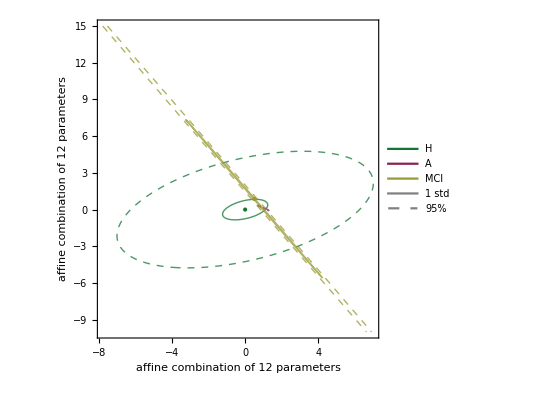

```mathematica
Show[Join[Array[cont,3],{centres}]]
```

```mathematica
expdf["std95_12_params_longM_"<>isodate]
```

../work/std95_12_params_longM_170318T0020.pdf

```mathematica
(* These are some scripts just to copy the data on the latex file *)Grid[Table[{"$"<>ToString[i+13*2]<>"$ & C & $("<>ToString[T[datafull[[2]]][[i]]]<>")$ \\\\"},{i,12} ]]
```

$27$ & C & $({0.575399, 1.84898, 0.596428, 140.973, 0.080927, 246})$ \\
$28$ & C & $({0.687646, 1.48628, 0.691763, 144.406, 0.04448, 211})$ \\
$29$ & C & $({0.576417, 1.81166, 0.583679, 129.694, 0.051219, 226})$ \\
$30$ & C & $({0.669721, 1.5166, 0.672916, 129.926, 0.032039, 195})$ \\
$31$ & C & $({0.736418, 1.36799, 0.73886, 145.074, 0.022411, 198})$ \\
$32$ & C & $({0.743739, 1.35582, 0.746371, 174.035, 0.024474, 235})$ \\
$33$ & C & $({0.664138, 1.55512, 0.673374, 156.736, 0.034872, 237})$ \\
$34$ & C & $({0.614609, 1.69503, 0.624112, 132.756, 0.045331, 217})$ \\
$35$ & C & $({0.439049, 2.31677, 0.478943, 131.715, 0.13096, 301})$ \\
$36$ & C & $({0.728062, 1.38382, 0.730246, 165.998, 0.021884, 229})$ \\
$37$ & C & $({0.719449, 1.4011, 0.721807, 161.157, 0.020809, 225})$ \\
$38$ & C & $({0.689622, 1.49152, 0.697921, 162.061, 0.044468, 236})$ \\

```mathematica
Table[If[i<=j,ToString[(datafull[[1]].T@datafull[[1]])[[i,j]]/Length[T@datafull[[1]]]],""],{i,6},{j,6}]//MF
```

(0.402114 | 1.03346 | 0.409205 | 100.371 | 0.0324141 | 156.968
 | 2.93548 | 1.05846 | 256.904 | 0.103465 | 420.29
 |  | 0.416651 | 102.093 | 0.0335846 | 160.097
 |  |  | 25222.8 | 7.99839 | 39366.2
 |  |  |  | 0.00433914 | 13.8298
 |  |  |  |  | 62677.3)

```mathematica
hh=2;Grid[
Table[
If[i≤j,ToString[(datafull[[hh]].T@datafull[[hh]])[[i,j]]/Length@T[datafull[[hh]]]],""]<>If[j<6," & "," \\\\"],{i,6},{j,6}]]
```

0.434586 &  | 1.0248 &  | 0.439879 &  | 97.5448 &  | 0.0277439 &  | 148.531 \\
 &  | 2.6401 &  | 1.04242 &  | 234.405 &  | 0.0817666 &  | 373.415 \\
 &  |  &  | 0.44537 &  | 98.8598 &  | 0.0284874 &  | 150.919 \\
 &  |  &  |  &  | 22091. &  | 6.58946 &  | 33961.6 \\
 &  |  &  |  &  |  &  | 0.00304913 &  | 11.2511 \\
 &  |  &  |  &  |  &  |  &  | 53432.3 \\

```mathematica
names
```

```mathematica
datafull[[1,1]]
```

{0.555869,0.525715,0.612931,0.578456,0.453708,0.678076,0.561081,0.736883,0.561073,0.694201,0.72678,0.706357,0.764527}

```mathematica
means[2]//N
```

{0.653689,1.60256,0.663035,147.878,0.0461562,229.667}

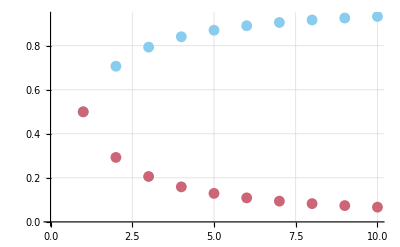

```mathematica
ListPlot[Evaluate@T@Table[{{n,2^(-1/n)},{n,1-2^(-1/n)}},{n,10}],GridLines->Auto]
```

```mathematica
{2^(-1/6),1-2^(-1/6)}//N
```

{0.890899,0.109101}

```mathematica
Solve[0.99^n==1/10,n]
```

{{n→229.105}}

```mathematica
(* error of maximum-likelihood *)
(13+1)/(13-1-6)//N
```

2.33333